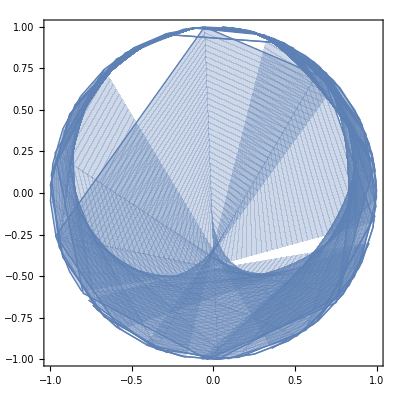

```mathematica
ClearAll["Global`*"];
r[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1}]
```